## Study the evolution of H(θ,φ;𝒫) w.r.t change of MOIs

## 𝒫 is the parameter set (V,γ, ℐ_1,ℐ_2,ℐ_3)

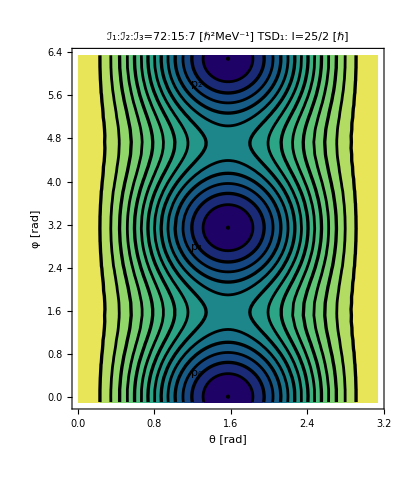

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1];
IF[X_]:=1/(2*X);
H[I_,θ_,φ_,A1_,A2_,A3_,V_,γ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ]^2(A1*Cos[φ]^2+A2*Sin[φ]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ]-V*(2j-1)/(j+1)Sin[γ+π/6];
CPH[spin_,I1_,I2_,I3_,V_,γ_,i_,bandName_]:=Show[ContourPlot[H[spin,θ,φ,IF[I1],IF[I2],IF[I3],V,γ*π/180]/.{j->13/2},{θ,0,π},{φ,-0.1,2.02π},AspectRatio->1.21,Contours->14,ContourStyle->{{Black,Thickness[0.005],Opacity[1]},{Black,Thick,Thickness[0.006],Opacity[1]}},Frame->True,ColorFunction->"BlueGreenYellow",Axes->False,FrameStyle->Directive[Thickness[0.005],Black],FrameLabel->{"θ [rad]","φ [rad]"},PlotLabel->Text[Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:`` [ℏ^2MeV^-1]\n            ``: I=`` [ℏ]"][I1,I2,I3,bandName,i],Black,FontFamily->"Times",21]],PlotLegends->BarLegend[Automatic,LegendMarkerSize->250,LegendFunction->"Frame",LegendMargins->4,LegendLabel->"ℋ(θ,φ)\n[MeV]"],LabelStyle->{Black,21,FontFamily->"Times"}],Epilog->{Inset[Framed[Style["p_0",18,Bold,FontFamily->"Times",Italic],Background->LightGray,FrameStyle->Black],Scaled[{0.4,0.1}]],Inset[Framed[Style["p_1",18,Bold,FontFamily->"Times",Italic],Background->LightGray,FrameStyle->Black],Scaled[{0.4,0.45}]],Inset[Framed[Style["p_2",18,Bold,FontFamily->"Times",Italic],Background->LightGray,FrameStyle->Black],Scaled[{0.4,0.9}]]}];
Show[CPH[12.5,72,15,7,2.1,22,"25/2","TSD_1"],Graphics[Style[Point[{{π/2,0}}],Red,PointSize[0.04]]],Graphics[Style[Point[{{π/2,π}}],Red,PointSize[0.04]]],Graphics[Style[Point[{{π/2,2π}}],Red,PointSize[0.04]]]]
```

```mathematica
GraphicsGrid[{{Show[CPH[12.5,72,15,7,2.1,22,"25/2"],Graphics[Style[Point[{{π/2,0}}],Red,PointSize[0.02]]],Graphics[Style[Point[{{π/2,π}}],Red,PointSize[0.02]]],Graphics[Style[Point[{{π/2,2π}}],Red,PointSize[0.02]]]],Show[CPH[15.5,72,15,7,2.1,22,"31/2"],Graphics[Style[Point[{{π/2,0}}],Red,PointSize[0.02]]],Graphics[Style[Point[{{π/2,π}}],Red,PointSize[0.02]]],Graphics[Style[Point[{{π/2,2π}}],Red,PointSize[0.02]]]]},{Show[CPH[18.5,72,15,7,2.1,22,"37/2"],Graphics[Style[Point[{{π/2,0}}],Red,PointSize[0.02]]],Graphics[Style[Point[{{π/2,π}}],Red,PointSize[0.02]]],Graphics[Style[Point[{{π/2,2π}}],Red,PointSize[0.02]]]],Show[CPH[25.5,72,15,7,2.1,22,"51/2"],Graphics[Style[Point[{{π/2,0}}],Red,PointSize[0.02]]],Graphics[Style[Point[{{π/2,π}}],Red,PointSize[0.02]]],Graphics[Style[Point[{{π/2,2π}}],Red,PointSize[0.02]]]]}},ImageSize->Scaled[1],Frame->All]
(*Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/Contours_grid_view.pdf",GraphicsGrid[{{CPH[12.5,72,15,7,2.1,22,"25/2"],CPH[12.5,72,15,7,2.1,22,"25/2"]},{CPH[12.5,72,15,7,2.1,22,"25/2"],CPH[12.5,72,15,7,2.1,22,"25/2"]}},ImageSize->Scaled[1],Frame->All]];*)
```

-Graphics-

```mathematica
pointSize=0.04;
```

## TSD1

```mathematica
pw1=Show[CPH[12.5,72,15,7,2.1,22,"25/2","TSD_1"],Graphics[Style[Point[{{π/2,0}}],Red,PointSize[pointSize]]],Graphics[Style[Point[{{π/2,π}}],Red,PointSize[pointSize]]],Graphics[Style[Point[{{π/2,2π}}],Red,PointSize[pointSize]]]];
Export["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Double_Shift_Formalism/Contour_Plots/contour-tsd1.pdf",pw1,ImageResolution->1300];
pw1
```

-Graphics-

## TSD2

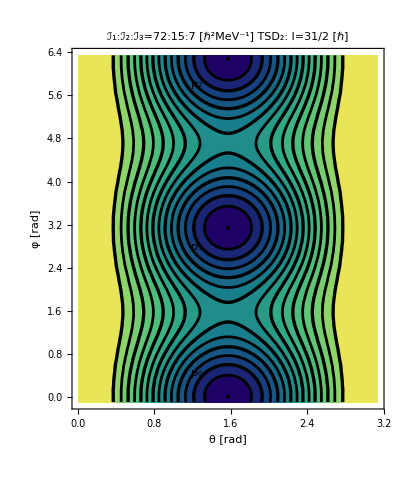

```mathematica
pw2=Show[CPH[15.5,72,15,7,2.1,22,"31/2","TSD_2"],Graphics[Style[Point[{{π/2,0}}],Red,PointSize[pointSize]]],Graphics[Style[Point[{{π/2,π}}],Red,PointSize[pointSize]]],Graphics[Style[Point[{{π/2,2π}}],Red,PointSize[pointSize]]]];
Export["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Double_Shift_Formalism/Contour_Plots/contour-tsd2.pdf",pw2];
pw2
```

## TSD3

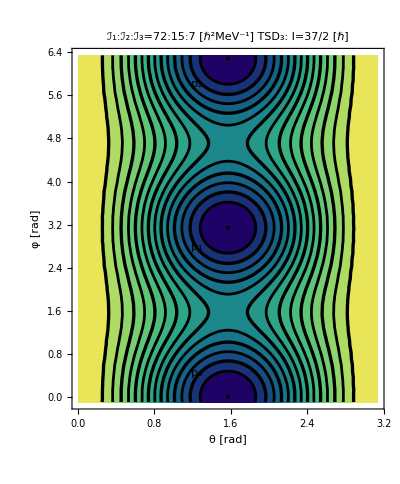

```mathematica
pw3=Show[CPH[18.5,72,15,7,2.1,22,"37/2","TSD_3"],Graphics[Style[Point[{{π/2,0}}],Red,PointSize[pointSize]]],Graphics[Style[Point[{{π/2,π}}],Red,PointSize[pointSize]]],Graphics[Style[Point[{{π/2,2π}}],Red,PointSize[pointSize]]]];
Export["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Double_Shift_Formalism/Contour_Plots/contour-tsd3.pdf",pw3];
pw3
```

## TSD4

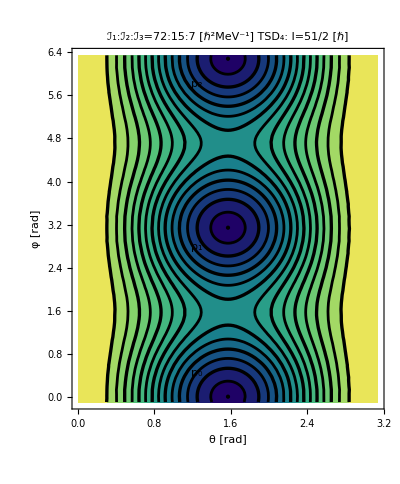

```mathematica
pw4=Show[CPH[25.5,72,15,7,2.1,22,"51/2","TSD_4"],Graphics[Style[Point[{{π/2,0}}],Red,PointSize[pointSize]]],Graphics[Style[Point[{{π/2,π}}],Red,PointSize[pointSize]]],Graphics[Style[Point[{{π/2,2π}}],Red,PointSize[pointSize]]]];
Export["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Double_Shift_Formalism/Contour_Plots/contour-tsd4.pdf",pw4];
pw4
```

## Make a graphics grid with the four spin values

### Parameters were obtained from the double-energy-shift fitting procedure

```mathematica
grid[I1_,I2_,I3_,I4_]:=GraphicsGrid[{{Show[CPH[I1,72,15,7,2.1,22]],Show[CPH[I2,72,15,7,2.1,22]]},{Show[CPH[I3,72,15,7,2.1,22]],Show[CPH[I4,72,15,7,2.1,22]]}},ImageSize->Scaled[2.5],Frame->All];
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/Contour-Grid_doubleShift.png",Show[grid[12.5,15.5,18.5,25.5]]];
```

## Separate contour plots for each spin value

## spin - 1

```mathematica
Show[CPH[12.5,72,15,7,2.1,22]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/Contour-Spin1_DS.png",Show[CPH[12.5,72,15,7,2.1,22]]];
```

-Graphics-

## spin - 2

```mathematica
Show[CPH[15.5,72,15,7,2.1,22]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/Contour-Spin2_DS.png",Show[CPH[15.5,72,15,7,2.1,22]]];
```

-Graphics-

```mathematica
Show[CPH[18.5,72,15,7,2.1,22]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/Contour-Spin3_DS.png",Show[CPH[18.5,72,15,7,2.1,22]]];
```

-Graphics-

```mathematica
Show[CPH[25.5,72,15,7,2.1,22]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/Contour-Spin4_DS.png",Show[CPH[25.5,72,15,7,2.1,22]]];
```

-Graphics-

```mathematica
(*Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Energy_Function/CP_animation_I2change.gif",Table[CPH[12.5,73,moi,3,8.1,19],{moi,3,73,0.5}]];*)
```

```mathematica
(*Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Energy_Function/CP_animation_I3change.gif",Table[CPH[12.5,73,3,moi,8.1,19],{moi,3,73,0.5}]];*)
```